```mathematica
SetDirectory[NotebookDirectory[]];
files=FileNames["energiea*"];
data=Flatten[Import[#,"Table"]]&/@files;
Dimensions[data]
data[[1]];
```

{12,1024}

```mathematica
n={1,2,3,4,5,6,7,8,9,10,11,12};
f={{0,60,100,1000,10,100,10,100,5,600,60,40},{0,20,100,3000,10,300,10,100,5,2000,200,40},{0,20,100,3000,10,300,10,100,5,2000,200,40},{0,20,100,3000,100,300,10,100,5,1800,260,40},{0,20,100,3000,200,300,10,100,5,1800,260,40},{0,20,100,5000,300,400,10,100,5,3000,350,40},{0,20,1000,5000,300,400,10,100,5,3000,350,40},{0,20,100,7000,10,700,10,100,5,4000,450,40},{0,20,100,7000,10,700,10,100,5,4000,450,40},{0,20,100,7000,10,700,10,100,5,4000,450,40},{0,20,100,7000,10,700,10,100,5,4000,450,40},{0,20,5000,6000,600,700,10,100,5,5500,600,40}};SetDirectory[NotebookDirectory[]];
files=FileNames["energiea*"];
data=Flatten[Import[#,"Table"]]&/@files;
Dimensions[data]
data[[1]];
nlms=NonlinearModelFit[data[[#]],{a+A Exp[-((x-μ)/σ)^2],f[[#,1]]<a,a<f[[#,2]],f[[#,3]]<A,A<f[[#,4]],f[[#,5]]<μ,μ<f[[#,6]],f[[#,7]]<σ,σ<f[[#,8]]},{{a,f[[#,9]]},{A,f[[#,10]]},{μ,f[[#,11]]},{σ,f[[#,12]]}},x]&/@n
Quiet[#["ParameterTable"]]&/@nlms
```

{FittedModel[39.7283+473.089 ⅇ^(-0.00404874 («1»)^2)],FittedModel[19.1782+1371.53 ⅇ^(-0.00171132 («1»)^2)],FittedModel[12.0183+1587.16 ⅇ^(-0.00122369 («1»)^2)],FittedModel[5.61072+1215.86 ⅇ^(-0.000933132 («1»)^2)],FittedModel[5.47567+1852.38 ⅇ^(-0.000741352 («1»)^2)],FittedModel[5.51936+2340.74 ⅇ^(-0.000644541 («1»)^2)],FittedModel[5.03364+2836.53 ⅇ^(-0.000567771 («1»)^2)],FittedModel[5.10022+3368.87 ⅇ^(-0.000506898 («1»)^2)],FittedModel[5.44147+4002.77 ⅇ^(-0.000451889 («1»)^2)],FittedModel[6.55662+4456.14 ⅇ^(-0.000418844 («1»)^2)],FittedModel[6.78354+5013.91 ⅇ^(-0.000379524 («1»)^2)],FittedModel[2.73835×10^-6+5468.71 ⅇ^(-0.000349442 («1»)^2)]}

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 39.7283 | 1.22684 | 32.3827 | 8.54665×10^-159
A | 473.089 | 10.5523 | 44.8326 | 2.18482×10^-243
μ | 59.9312 | 0.285252 | 210.1 | 7.16258513809×10^-842
σ | 15.7159 | 0.407503 | 38.5664 | 1.97448×10^-201, | Estimate | Standard Error | t-Statistic | P-Value
a | 19.1782 | 0.744873 | 25.7469 | 4.95459×10^-113
A | 1371.53 | 5.09019 | 269.446 | 4.12794283421×10^-950
μ | 110.669 | 0.0728585 | 1518.95 | 3.24258295419×10^-1713
σ | 24.1732 | 0.104697 | 230.888 | 8.3316360432×10^-883, | Estimate | Standard Error | t-Statistic | P-Value
a | 12.0183 | 0.561101 | 21.4192 | 2.43158×10^-84
A | 1587.16 | 3.49829 | 453.695 | 6.16956834832×10^-1179
μ | 149.043 | 0.0511145 | 2915.86 | 4.95020477257×10^-2002
σ | 28.5868 | 0.0736862 | 387.953 | 5.42304342798×10^-1110, | Estimate | Standard Error | t-Statistic | P-Value
a | 5.61072 | 0.369177 | 15.1979 | 3.56123×10^-47
A | 1215.86 | 2.13476 | 569.555 | 2.7719537212×10^-1279
μ | 198.983 | 0.0465775 | 4272.1 | 3.29154340502×10^-2171
σ | 32.7362 | 0.0673537 | 486.035 | 2.69027702429×10^-1209, | Estimate | Standard Error | t-Statistic | P-Value
a | 5.47567 | 0.467853 | 11.7038 | 8.86683×10^-30
A | 1852.38 | 2.53545 | 730.593 | 2.58184336541×10^-1389
μ | 260.593 | 0.0406947 | 6403.62 | 1.67580282177×10^-2350
σ | 36.7272 | 0.0590272 | 622.208 | 2.43769593105×10^-1318, | Estimate | Standard Error | t-Statistic | P-Value
a | 5.51936 | 0.555816 | 9.93018 | 3.02597×10^-22
A | 2340.74 | 2.8942 | 808.769 | 2.86810670246×10^-1434
μ | 304.14 | 0.039397 | 7719.89 | 2.60865876913×10^-2433
σ | 39.389 | 0.0572643 | 687.845 | 1.16523832572×10^-1362, | Estimate | Standard Error | t-Statistic | P-Value
a | 5.03364 | 0.553894 | 9.08772 | 5.13772×10^-19
A | 2836.53 | 2.78066 | 1020.09 | 5.68306343097×10^-1537
μ | 348.533 | 0.0332565 | 10480.1 | 1.01797400214×10^-2568
σ | 41.9675 | 0.0484388 | 866.404 | 1.0191942454×10^-1464, | Estimate | Standard Error | t-Statistic | P-Value
a | 5.10022 | 0.67652 | 7.5389 | 1.04468×10^-13
A | 3368.87 | 3.286 | 1025.22 | 3.44060438293×10^-1539
μ | 396.945 | 0.0349967 | 11342.4 | 9.64216498586×10^-2604
σ | 44.416 | 0.0510749 | 869.626 | 2.3249118946×10^-1466, | Estimate | Standard Error | t-Statistic | P-Value
a | 5.44147 | 0.718324 | 7.57523 | 8.01991×10^-14
A | 4002.77 | 3.37325 | 1186.62 | 6.66888918731×10^-1604
μ | 449.734 | 0.0319996 | 14054.3 | 1.03757032114×10^-2698
σ | 47.0418 | 0.0468026 | 1005.11 | 2.00678004934×10^-1530, | Estimate | Standard Error | t-Statistic | P-Value
a | 6.55662 | 0.837923 | 7.82485 | 1.26597×10^-14
A | 4456.14 | 3.84731 | 1158.25 | 3.45153527114×10^-1593
μ | 495.163 | 0.0340341 | 14549. | 4.92749055334×10^-2714
σ | 48.8623 | 0.0498546 | 980.096 | 2.84977071579×10^-1519, | Estimate | Standard Error | t-Statistic | P-Value
a | 6.78354 | 0.807429 | 8.40141 | 1.46576×10^-16
A | 5013.91 | 3.59967 | 1392.88 | 7.49016025627×10^-1675
μ | 553.075 | 0.029709 | 18616.4 | 3.08024988079×10^-2823
σ | 51.3311 | 0.0436109 | 1177.03 | 2.62626934057×10^-1600, | Estimate | Standard Error | t-Statistic | P-Value
a | 2.73835×10^-6 | 4.13814 | 6.61734×10^-7 | 0.999999
A | 5468.71 | 17.9948 | 303.905 | 9.13102777388×10^-1003
μ | 609.045 | 0.141811 | 4294.77 | 1.48814747128×10^-2173
σ | 53.4949 | 0.208561 | 256.495 | 1.31573615605×10^-928}

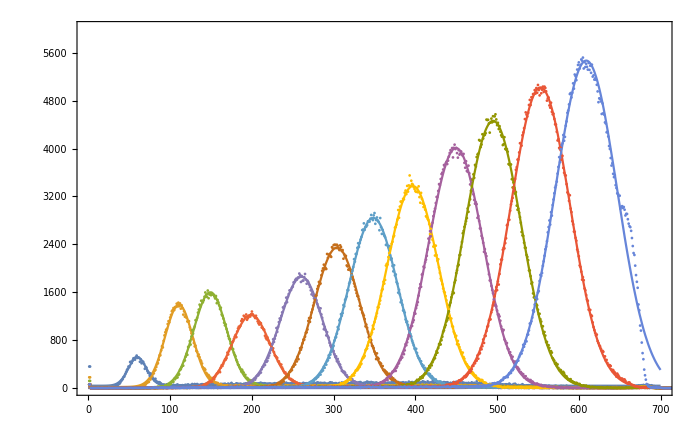

```mathematica
Show[Plot[Evaluate[Normal[#]&/@nlms],{x,0,700},PlotRange->{0,6000},Frame->True,ImageSize->700],ListPlot[#&/@data]]
```

```mathematica
as=Quiet[#["ParameterTableEntries"][[1,1]]]&/@nlms
As=Quiet[#["ParameterTableEntries"][[2,1]]]&/@nlms
mues=Quiet[#["ParameterTableEntries"][[3,1]]]&/@nlms
sigmas=Quiet[#["ParameterTableEntries"][[4,1]]]&/@nlms

smdata=Transpose[{mues,sigmas}];
```

{39.7283,19.1782,12.0183,5.61072,5.47567,5.51936,5.03364,5.10022,5.44147,6.55662,6.78354,2.73835×10^-6}

{473.089,1371.53,1587.16,1215.86,1852.38,2340.74,2836.53,3368.87,4002.77,4456.14,5013.91,5468.71}

{59.9312,110.669,149.043,198.983,260.593,304.14,348.533,396.945,449.734,495.163,553.075,609.045}

{15.7159,24.1732,28.5868,32.7362,36.7272,39.389,41.9675,44.416,47.0418,48.8623,51.3311,53.4949}

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.31463 | 0.999935 | 1.31472 | 0.217958
b | 2.15284 | 0.0552132 | 38.9915 | 2.94005×10^-12

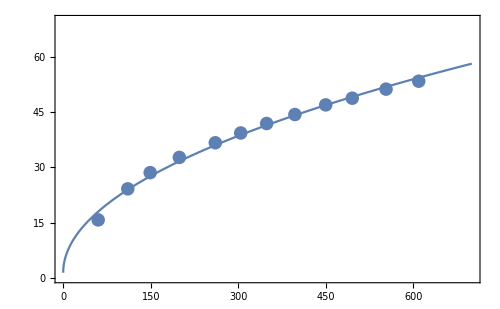

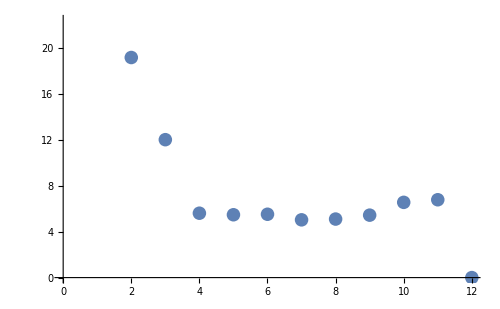

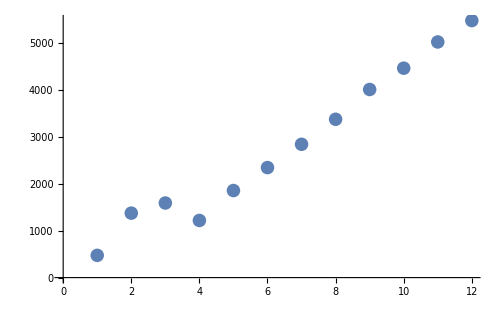

```mathematica
nlmsm=NonlinearModelFit[smdata,{a +b x^0.5},{a,b},x];
Quiet[nlmsm["ParameterTable"]]

Show[Plot[Normal[nlmsm],{x,0,700},PlotRange->{0,70},Frame->True,ImageSize->500],ListPlot[smdata]]

ListPlot[as]
ListPlot[As]
```

```mathematica
Series[√x,{x,0,5}]
```

√x+O[x]^(11/2)